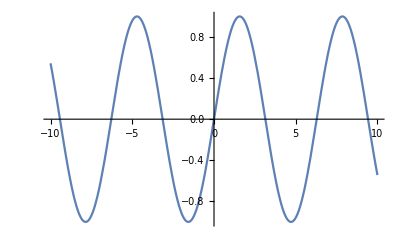

```mathematica
f[x_]:= Sin[x];
Plot[f[i],{i,-10,10}] (* value, min, max *)
```

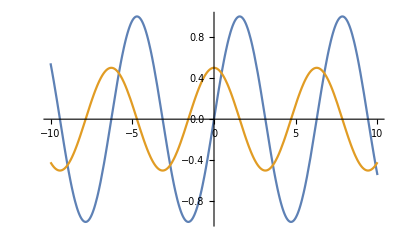

```mathematica
(*Now add new function*)
g[x_]:=1/2 Cos[x];
Plot[ {f[i],g[i]},{i,-10,10}](* And plot together *)
```

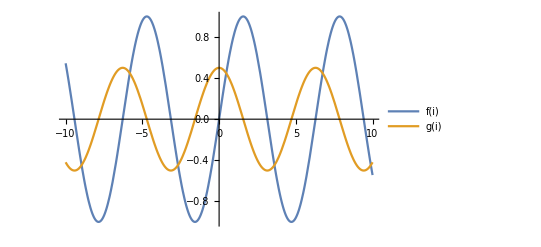

```mathematica
(*so, let's add legends:P *)
Plot[ {f[i],g[i]},{i,-10,10},
PlotLegends->"Expressions"](* or let's see other properties of PlotLegends *)
```

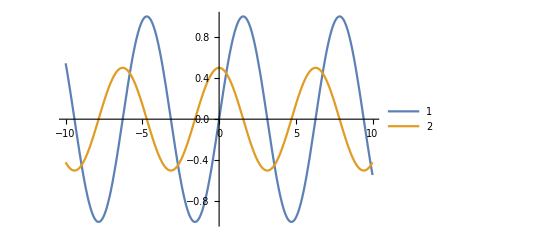

```mathematica
Plot[ {f[i],g[i]},{i,-10,10},PlotLegends->Automatic]
```

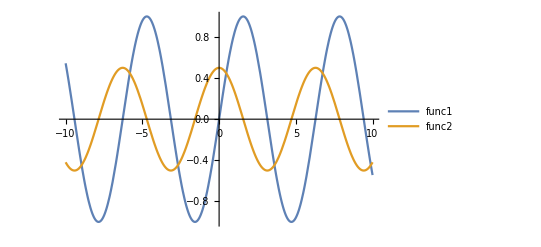

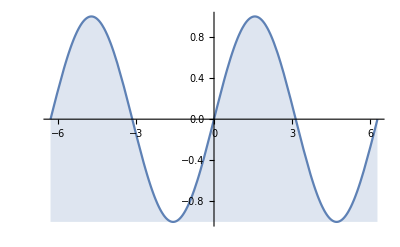

```mathematica
(*sweety, The last one is *)
Plot[ {f[i],g[i]},{i,-10,10},PlotLegends->{func1,func2}]





(*Jolly well, let's paint area about the curve*)
Plot[f[x],{x,-2π,2π},Filling->Bottom]
```

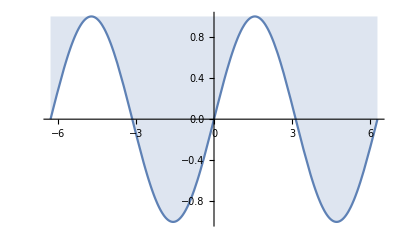

```mathematica
Plot[f[x],{x,-2π,2π},Filling->Top]
```

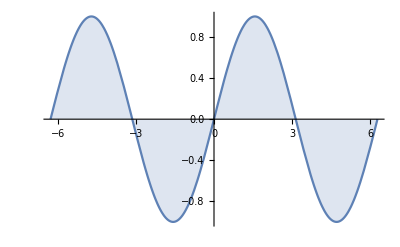

```mathematica
Plot[f[x],{x,-2π,2π},Filling->Axis]
```

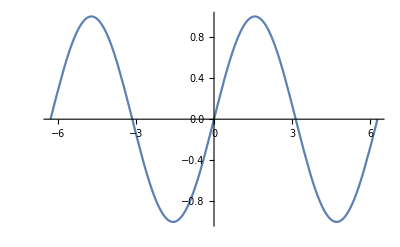

```mathematica
Plot[f[x],{x,-2π,2π},Filling->None]
```

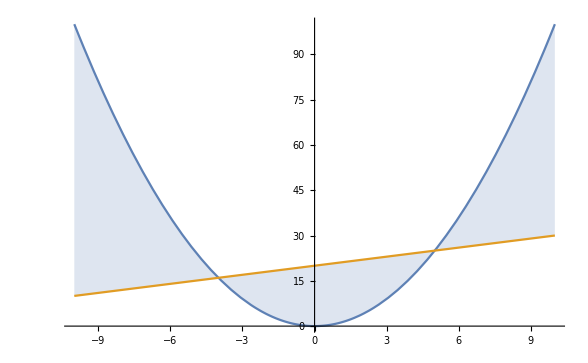

```mathematica
(*
	create a simple set of functions
*)
Plot[{x^2,1x+20},{x,-10,10},Filling->{1->{2}}]
```

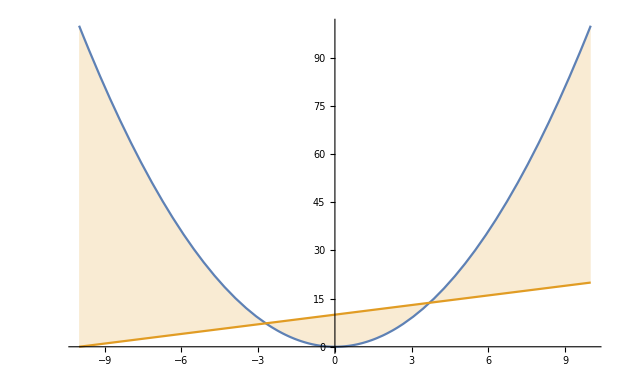

```mathematica
Plot[{x^2,1x+10},{x,-10,10},Filling->{2->{1}}]
```

```mathematica
(*
	so,lad turn back to our function of sin x
*)
```

```mathematica
Plot[f[i],{i,-2π,2π}]
```

-Graphics-

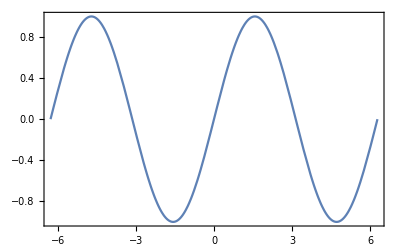

```mathematica
(*let's create a frame*)
Plot[f[i],{i,-2π,2π},Frame->True]
```

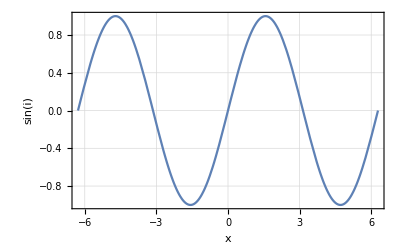

```mathematica
(*
	try this: Frame->False and Frame->None
	i wanna a a grid and name of x,y
*)

Plot[f[i],{i,-2π,2π},Frame->True,GridLines->Automatic,AxesLabel->{x,f[x]}]
```

```mathematica
(*or custom gridlines*)
```

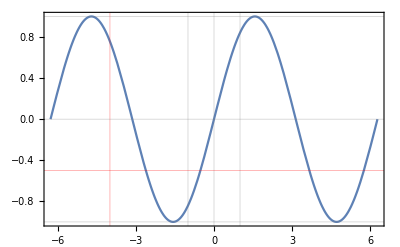

```mathematica
Plot[f[i],{i,-2π,2π},Frame->True,GridLines->{{{-4,Red},-1,0,1}, {-1,{-.5,Red},0,1}}]
```

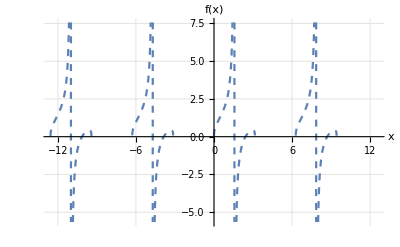

```mathematica
Plot[Tan[x]+Sin[x]^.3,{x,-4π,4π},AxesLabel->{"x","f(x)"},Axes->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Red],PlotStyle->Dashed]
```